```mathematica
Clear["Global`*"]
```

```mathematica
(*初始化函数*)
initialization[pop_,ub_,lb_,dim_]:=(
X=Table[0,{i,1,pop},{j,1,dim}];
Do[X[[i,j]]=(ub[[j]]-lb[[j]])*RandomReal[]+lb[[j]],{i,1,pop},{j,1,dim}];
X
)
```

```mathematica
(*边界检查函数*)
boundaryCheck[x_,ub_,lb_,dim_]:=Module[{xNew=x},
Do[
If[xNew[[i]]>ub[[i]],xNew[[i]]=ub[[i]]];
If[xNew[[i]]<lb[[i]],xNew[[i]]=lb[[i]]];
,{i,1,Length[xNew]}];
xNew
]
```

```mathematica
(*蜉蝣优化算法函数，pop为种群数量，dim为每个个体维度，ub为上边界信息，lb为下边界信息，fobj为适应度函数接口，maxiter为算法最大迭代次数*)
MOA[pop_,dim_,ub_,lb_,fobj_,maxiter_]:=(
(*雄性蜉蝣数量*)
npop=pop;
(*雌性蜉蝣数量*)
npopf=pop;
(*初始化迭代列表*)
itercurve=Table[0,{i,1,maxiter}];
(*速度最值*)
velmax=0.1*(ub-lb);
velmin=-velmax;
(*雄性蜉蝣种群初始化*)
mayfly=initialization[npop,ub,lb,dim];
(*计算适应度*)
fitness=Table[fobj[mayfly[[i,;;]]],{i,1,npop}];
(*雄性速度初始化*)
mayflyv=initialization[npop,velmax,velmin,dim];
(*获取雄性种群最优个体及适应度*)
{fitnessbest,indexmin}={Min[fitness],Ordering[fitness][[1]]};
mayflybest=mayfly[[indexmin,;;]];
(*记录历史最优位置*)
mayflypbest=mayfly;
mayflypfitness=fitness;
(*雌性种群初始化*)
mayflyf=initialization[npopf,ub,lb,dim];
(*计算适应度*)
fitnessf=Table[fobj[mayflyf[[i,;;]]],{i,1,npop}];
(*雌性速度初始化*)
mayflyfv=initialization[npopf,velmax,velmin,dim];
(*获取雌性种群最优个体及适应度*)
{fitnessbestf,indexminf}={Min[fitnessf],Ordering[fitnessf][[1]]};
mayflybestf=mayflyf[[indexminf,;;]];
(*记录最优解*)
bestfitness=Infinity;
bestpos=Table[0,{i,1,Length[dim]}];
If[fitnessbest<bestfitness,
bestfitness=fitnessbest;
bestpos=mayflybest];
If[fitnessbestf<bestfitness,
bestfitness=fitnessbestf;
bestpos=mayflybestf];
(*迭代*)
Do[
(*更新雄性历史最优*)
Do[
If[fitness[[i]]<mayflypfitness[[i]],
mayflypfitness[[i]]=fitness[[i]];
mayflypbest[[i,;;]]=mayfly[[i,;;]]];
,{i,1,npop}];
(*更新雄性*)
Do[
rpbest=Norm[mayflypbest[[i,;;]]-mayfly[[i,;;]]];
rgbest=Norm[mayflybest-mayfly[[i,;;]]];
e=2*RandomReal[{0,1},{1,dim}]-1;
If[fitness[[i]]>fitnessbest,
mayflyv[[i]]=N[g*mayflyv[[i]]+a1*Exp[-beta*rpbest^2]*(mayflypbest[[i]]-mayfly[[i]])+a2*Exp[-beta*rgbest^2]*(mayflybest-mayfly[[i]]),50],
mayflyv[[i]]=mayflyv[[i]]+dance*e[[1]]];
(*速度边界检查*)
mayflyv[[i]]=boundaryCheck[mayflyv[[i]],velmax,velmin,dim];
(*位置更新*)
mayfly[[i]]=mayfly[[i]]+mayflyv[[i]];
(*位置边界检查*)
mayfly[[i]]=boundaryCheck[mayfly[[i]],ub,lb,dim];
(*适应度计算*)
fitness[[i]]=fobj[mayfly[[i]]];
If[fitness[[i]]<fitnessbest,
fitnessbest=fitness[[i]];
mayflybest=mayfly[[i]]];
,{i,1,npop}];
(*更新雌性*)
Do[
e=2*RandomReal[{0,1},{1,dim}]-1;
(*速度更新*)
If[fitnessf[[i]]>fitness[[i]],
rmf=Norm[mayfly[[i]]-mayflyf[[i]]];
mayflyfv[[i]]=g*mayflyfv[[i]]+a3*Exp[-beta*rmf^2]*(mayfly[[i]]-mayflyf[[i]]),
mayflyfv[[i]]=g*mayflyfv[[i]]+fl*e[[1]]];
(*速度边界检查*)
mayflyfv[[i]]=boundaryCheck[mayflyfv[[i]],velmax,velmin,dim];
(*位置更新*)
mayflyf[[i]]=mayflyf[[i]]+mayflyfv[[i]];
(*位置边界检查*)
mayflyf[[i]]=boundaryCheck[mayflyf[[i]],ub,lb,dim];
(*适应度计算*)
fitnessf[[i]]=fobj[mayflyf[[i]]];
If[fitnessf[[i]]<fitnessbestf,
fitnessbestf=fitnessf[[i]];
mayflybestf=mayflyf[[i,;;]]]
,{i,1,npopf}];
(*更新全局最优*)
If[fitnessbest<bestfitness,
bestfitness=fitnessbest;
bestpos=mayflybest];
If[fitnessbestf<bestfitness,
bestfitness=fitnessbestf;
bestpos=mayflybestf];
(*排序*)
sortindex=Ordering[fitness];
sortindexf=Ordering[fitnessf];
(*交配列表初始化*)
mayflyoffspring=Table[0,{i,1,nc},{j,1,dim}];
fitnessoffspring=Table[0,{i,1,nc}];
Do[
L=2*RandomReal[{0,1},{1,dim}]-1;
(*交配*)
mayflyoffspring[[k]]=L[[1]]*mayfly[[sortindex[[k]]]]+(1-L[[1]])*mayflyf[[sortindex[[k]]]];
(*边界检查*)
mayflyoffspring[[k]]=boundaryCheck[mayflyoffspring[[k]],ub,lb,dim];
fitnessoffspring[[k]]=fobj[mayflyoffspring[[k]]];
(*计算适应度，跟本代雄性雌性比较，如果更优，则替换原始雄性雌性*)
If[fitnessoffspring[[k]]<fitness[[sortindex[[k]]]],
mayfly[[sortindex[[k]]]]=mayflyoffspring[[k]];
fitness[[sortindex[[k]]]]=fitnessoffspring[[k]]];
If[fitnessoffspring[[k]]<fitnessf[[sortindex[[k]]]],
mayflyf[[sortindex[[k]]]]=mayflyoffspring[[k+1]];
fitnessf[[sortindex[[k]]]]=fitnessoffspring[[k+1]]];
L=2*RandomReal[{0,1},{1,dim}]-1;
(*交配*)
mayflyoffspring[[k+1]]=L[[1]]*mayflyf[[sortindex[[k]]]]+(1-L[[1]])*mayfly[[sortindex[[k]]]];
(*边界检查*)
mayflyoffspring[[k+1]]=boundaryCheck[mayflyoffspring[[k+1]],ub,lb,dim];
fitnessoffspring[[k+1]]=fobj[mayflyoffspring[[k+1]]];
If[fitnessoffspring[[k+1]]<fitnessf[[sortindexf[[k]]]],
mayflyf[[sortindexf[[k]]]]=mayflyoffspring[[k+1]];
fitnessf[[sortindex[[k]]]]=fitnessoffspring[[k+1]]];
(*计算适应度，跟本代雄性雌性比较，如果更优，则替换原始雄性雌性*)
If[fitnessoffspring[[k+1]]<fitnessf[[sortindex[[k]]]],
mayfly[[sortindex[[k]]]]=mayflyoffspring[[k+1]];
fitness[[sortindex[[k]]]]=fitnessoffspring[[k+1]]]
,{k,1,nc,2}];
(*寻找子代最小适应度*)
{minfitoffspring,minindexoffspring}={Min[fitnessoffspring],Ordering[fitnessoffspring][[1]]};
(*如果比全局更优，则替换全局最优*)
If[minfitoffspring<bestfitness,
bestfitness=minfitoffspring;
bestpos=mayflyoffspring[[minindexoffspring,;;]]];
itercurve[[t]]=bestfitness;
,{t,1,maxiter}];
{bestpos,bestfitness,itercurve})
```

```mathematica
(*适应度函数，实际问题中更换为主函数*)
(*fun[x_]:=Module[{fitness},fitness=x[[1]]^2+x[[2]]^2]*)
```

```mathematica
dataneed=Part[Import@"C:\\Users\\PC\\Desktop\\电工杯\\赛题以及数据A\\附件1：各园区典型日负荷数据.csv",2;;];
(*A地负荷*)dataAneed=1.5*Drop[#2&@@@dataneed,-2];
(*B地负荷*)dataBneed=1.5*Drop[#3&@@@dataneed,-2];
(*C地负荷*)dataCneed=1.5*Drop[#4&@@@dataneed,-2];
dataproduce=Part[Import@"C:\\Users\\PC\\Desktop\\电工杯\\赛题以及数据A\\附件2：各园区典型日风光发电数据.csv",4;;];
(*A地发电量*)dataAproduce=750*#2&@@@dataproduce;
(*B地发电量*)dataBproduce=1000*#3&@@@dataproduce;
(*C地光能发电量*)dataCproducelight=600*#4&@@@dataproduce;
(*C地风能发电量*)dataCproducewind=500*#5&@@@dataproduce;
```

```mathematica
(*电工杯测试函数*)
moneyC=ebuynetC=ebuywindC=ebuylightC=wasteC=Table[i,{i,24}];
daypriceC=Table[i,{i,1825}];
saveC=Table[i,{i,25}];
findminC[{power_?NumericQ,energy_?NumericQ,pv_?NumericQ,pw_?NumericQ}]:=
Module[{sumpriceC},
(*C地光能发电量*)dataCproducelight=pv*#4&@@@dataproduce;
(*C地风能发电量*)dataCproducewind=pw*#5&@@@dataproduce;
saveC[[1]]=energy*0.1;
Do[
Do[
If[dataCneed[[hour]]<dataCproducelight[[hour]],
ebuylightC[[hour]]=dataCneed[[hour]];
ebuywindC[[hour]]=0;
ebuynetC[[hour]]=0;
wasteC[[hour]]=dataCproducelight[[hour]]+dataCproducewind[[hour]]-dataCneed[[hour]]-Min[{(dataCproducelight[[hour]]+dataCproducewind[[hour]]-dataCneed[[hour]]),power}];
moneyC[[hour]]=0.4*ebuylightC[[hour]]+0.5*ebuywindC[[hour]]+1*ebuynetC[[hour]];
saveC[[hour+1]]=saveC[[hour]]+Min[{(dataCproducelight[[hour]]+dataCproducewind[[hour]]-dataCneed[[hour]]),power}]];
If[dataCproducelight[[hour]]<=dataCneed[[hour]]<dataCproducelight[[hour]]+dataCproducewind[[hour]],
ebuylightC[[hour]]=dataCproducelight[[hour]];
ebuywindC[[hour]]=dataCneed[[hour]]-dataCproducelight[[hour]];
ebuynetC[[hour]]=0;
wasteC[[hour]]=dataCproducelight[[hour]]+dataCproducewind[[hour]]-dataCneed[[hour]]-Min[{(dataCproducelight[[hour]]+dataCproducewind[[hour]]-dataCneed[[hour]]),power}];
moneyC[[hour]]=0.4*ebuylightC[[hour]]+0.5*ebuywindC[[hour]]+1*ebuynetC[[hour]];
saveC[[hour+1]]=saveC[[hour]]+Min[{(dataCproducelight[[hour]]+dataCproducewind[[hour]]-dataCneed[[hour]]),power}]];
If[dataCproducelight[[hour]]+dataCproducewind[[hour]]<=dataCneed[[hour]]<dataCproducelight[[hour]]+dataCproducewind[[hour]]+(saveC[[hour]]-energy*0.1)*0.95,
ebuylightC[[hour]]=dataCproducelight[[hour]];
ebuywindC[[hour]]=dataCproducewind[[hour]];
ebuynetC[[hour]]=0;
wasteC[[hour]]=0;
moneyC[[hour]]=0.4*ebuylightC[[hour]]+0.5*ebuywindC[[hour]]+1*ebuynetC[[hour]];
saveC[[hour+1]]=saveC[[hour]]-(dataCneed[[hour]]-dataCproducelight[[hour]]-dataCproducewind[[hour]])/0.95];
If[dataCneed[[hour]]>=dataCproducelight[[hour]]+dataCproducewind[[hour]]+(saveC[[hour]]-energy*0.1)*0.95,
ebuylightC[[hour]]=dataCproducelight[[hour]];
ebuywindC[[hour]]=dataCproducewind[[hour]];
ebuynetC[[hour]]=dataCneed[[hour]]-dataCproducelight[[hour]]-dataCproducewind[[hour]]-(saveC[[hour]]-energy*0.1)*0.95;
wasteC[[hour]]=0;
moneyC[[hour]]=0.4*ebuylightC[[hour]]+0.5*ebuywindC[[hour]]+1*ebuynetC[[hour]];
saveC[[hour+1]]=energy*0.1];
If[saveC[[hour+1]]>energy*0.9,saveC[[hour+1]]=energy*0.9];
,{hour,1,24}];
daypriceC[[day]]=Sum[moneyC[[hour]],{hour,1,24}];
saveC[[1]]=saveC[[25]];
,{day,1,1825}];
(*C地五年购电总成本*)sumpriceC=N[Sum[daypriceC[[day]],{day,1,1825}]+800*power+1800*energy+2500*pv+3000*pw,16]
]
```

```mathematica
(*惯性权重，原值：0.8*)
g=0.8;
(*雄性蜉蝣移动行为的个体最优吸引系数，原值：1*)
a1=1;
(*雄性蜉蝣移动行为的全局历史最优吸引系数，原值：1.5*)
a2=1.5;
(*雌性蜉蝣移动行为的吸引系数，原值：1.5*)
a3=1.5;
(*能见度系数，原值：2，推荐修改，目前数值为求解较快的经验值*)
beta=1/Mean[(ub-lb)^2];
(*舞蹈系数，原值：5，不推荐修改*)
dance=5;
(*随机游走系数，原值：1，不推荐修改*)
fl=1;
(*子代数量，原值：20，推荐修改*)
nc=10;
(*种群数量，原值：50，推荐修改*)
pop=20;
(*变量维度*)
dim=4;
(*个体上边界信息*)
ub={1000,1800,1500,2000};
(*个体下边界信息*)
lb={0,0,0,0};
(*最大迭代次数*)
maxiter=30;
(*将主函数与适应度函数连接*)
fobj=findminC;
(*求解最优个体信息，最优值，最优值迭代历史记录，计算时同步显示迭代次数*)
Monitor[{bestpos,bestfitness,itercurve}=MOA[pop,dim,ub,lb,fobj,maxiter],{bestpos,bestfitness,t}]
```

$Aborted

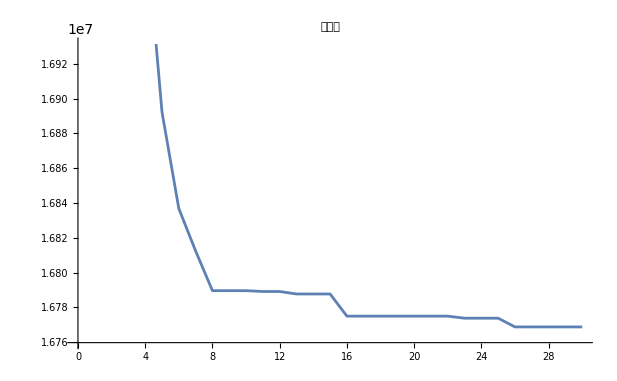

```mathematica
ListLinePlot[itercurve,PlotLabel->"适应度"]
```